```mathematica
image=-Graphics-;
image2=-Graphics-;
image3=-Graphics-;
--<
liste=PixelValuePositions[image,Black]
kor=CoordinateBounds[liste];

xmin=SortBy[kor,Last]⟦-1,1⟧;
xmax=SortBy[kor,Last]⟦-1,2⟧;
ymin=SortBy[kor,Last]⟦1,1⟧;
ymax=SortBy[kor,Last]⟦1,2⟧;

tepex=Part[liste]⟦1,1⟧;
cukurx=Part[liste]⟦-1,1⟧;

piuzunlugu=tepex-cukurx;
grfcuzunluk=xmax-xmin;

pisayısı=Floor[grfcuzunluk/piuzunlugu];

poz=Position[{liste},1,ymin,1];
poz=Part[poz]⟦1,2⟧;
tepex2=SortBy[liste]⟦1,1,1⟧;
cukurx2=SortBy[liste]⟦1,poz,-1⟧;

Print[xmin]
Print[xmax]
                                           Print[tepex]
Print[cukurx]
Print[piuzunlugu] 
Print[grfcuzunluk]
Print[pisayısı]
```

{{320,247},{322,247},{323,247},{151,246},{152,246},{153,246},{154,246},{155,246},{316,246},{317,246},{324,246},{149,245},{152,245},{155,245},{157,245},{158,245},{318,245},{323,245},{326,245},{148,244},{149,244},{150,244},{157,244},{159,244},{313,244},{314,244},{325,244},{326,244},{146,243},{147,243},{149,243},{156,243},{158,243},{160,243},{312,243},{314,243},{327,243},{148,242},{159,242},{161,242},{311,242},{313,242},{314,242},{327,242},{329,242},{146,241},{147,241},{159,241},{160,241},{162,241},{311,241},{328,241},{330,241},{144,240},{146,240},{160,240},{161,240},{163,240},{329,240},{330,240},{143,239},{145,239},{162,239},{163,239},{310,239},{330,239},{143,238},{144,238},{161,238},{309,238},{330,238},{332,238},{163,237},{164,237},{165,237},{308,237},{331,237},{142,236},{163,236},{307,236},{308,236},{333,236},{140,235},{141,235},{164,235},{165,235},{308,235},{332,235},{141,234},{307,234},{333,234},{334,234},{140,233},{165,233},{167,233},{334,233},{140,232},{165,232},{306,232},{333,232},{334,232},{140,231},{166,231},{167,231},{306,231},{335,231},{138,230},{167,230},{168,230},{304,230},{305,230},{335,230},{1,229},{137,229},{167,229},{169,229},{305,229},{336,229},{1,228},{137,228},{167,228},{168,228},{169,228},{303,228},{305,228},{337,228},{1,227},{136,227},{138,227},{168,227},{169,227},{304,227},{2,226},{137,226},{168,226},{170,226},{302,226},{336,226},{338,226},{2,225},{135,225},{170,225},{302,225},{337,225},{338,225},{2,224},{135,224},{169,224},{303,224},{337,224},{338,224},{2,223},{3,223},{134,223},{136,223},{170,223},{172,223},{302,223},{339,223},{3,222},{4,222},{134,222},{135,222},{170,222},{171,222},{172,222},{300,222},{340,222},{133,221},{173,221},{300,221},{340,221},{134,220},{172,220},{300,220},{301,220},{339,220},{4,219},{132,219},{133,219},{134,219},{173,219},{174,219},{299,219},{341,219},{5,218},{6,218},{132,218},{133,218},{172,218},{298,218},{299,218},{300,218},{340,218},{342,218},{131,217},{133,217},{172,217},{173,217},{175,217},{299,217},{342,217},{5,216},{6,216},{131,216},{174,216},{297,216},{341,216},{342,216},{7,215},{130,215},{132,215},{173,215},{298,215},{343,215},{7,214},{131,214},{176,214},{297,214},{8,213},{129,213},{131,213},{174,213},{176,213},{296,213},{342,213},{344,213},{130,212},{175,212},{176,212},{177,212},{297,212},{9,211},{129,211},{175,211},{295,211},{296,211},{343,211},{345,211},{8,210},{130,210},{178,210},{295,210},{9,209},{128,209},{177,209},{178,209},{296,209},{344,209},{346,209},{9,208},{127,208},{129,208},{178,208},{294,208},{295,208},{345,208},{9,207},{11,207},{177,207},{179,207},{346,207},{10,206},{127,206},{179,206},{293,206},{294,206},{295,206},{10,205},{11,205},{12,205},{126,205},{128,205},{178,205},{293,205},{294,205},{346,205},{347,205},{11,204},{178,204},{180,204},{346,204},{12,203},{125,203},{127,203},{179,203},{293,203},{294,203},{346,203},{348,203},{11,202},{13,202},{125,202},{180,202},{181,202},{347,202},{12,201},{125,201},{179,201},{181,201},{292,201},{348,201},{12,200},{13,200},{125,200},{126,200},{181,200},{124,199},{182,199},{291,199},{348,199},{13,198},{14,198},{124,198},{180,198},{181,198},{292,198},{349,198},{350,198},{13,197},{14,197},{125,197},{181,197},{182,197},{290,197},{349,197},{14,196},{123,196},{183,196},{290,196},{350,196},{124,195},{183,195},{349,195},{351,195},{14,194},{15,194},{183,194},{289,194},{290,194},{351,194},{16,193},{122,193},{182,193},{184,193},{290,193},{350,193},{16,192},{122,192},{123,192},{183,192},{289,192},{351,192},{15,191},{121,191},{182,191},{183,191},{288,191},{350,191},{351,191},{15,190},{17,190},{122,190},{184,190},{185,190},{288,190},{289,190},{352,190},{183,189},{287,189},{351,189},{16,188},{120,188},{122,188},{183,188},{287,188},{351,188},{17,187},{121,187},{184,187},{185,187},{288,187},{352,187},{353,187},{119,186},{184,186},{286,186},{287,186},{352,186},{17,185},{119,185},{120,185},{185,185},{287,185},{353,185},{17,184},{119,184},{120,184},{187,184},{286,184},{354,184},{18,183},{119,183},{185,183},{186,183},{287,183},{354,183},{19,182},{118,182},{187,182},{285,182},{287,182},{353,182},{18,181},{20,181},{120,181},{185,181},{186,181},{286,181},{353,181},{355,181},{19,180},{118,180},{119,180},{186,180},{188,180},{285,180},{20,179},{117,179},{285,179},{286,179},{354,179},{19,178},{20,178},{119,178},{186,178},{187,178},{284,178},{354,178},{356,178},{19,177},{21,177},{117,177},{118,177},{189,177},{355,177},{356,177},{20,176},{116,176},{117,176},{187,176},{283,176},{356,176},{20,175},{118,175},{188,175},{283,175},{357,175},{20,174},{116,174},{117,174},{188,174},{189,174},{356,174},{21,173},{116,173},{188,173},{283,173},{356,173},{22,172},{115,172},{190,172},{282,172},{284,172},{357,172},{23,171},{117,171},{188,171},{189,171},{283,171},{357,171},{21,170},{116,170},{190,170},{282,170},{283,170},{357,170},{22,169},{23,169},{115,169},{189,169},{191,169},{281,169},{283,169},{22,168},{23,168},{114,168},{115,168},{191,168},{281,168},{283,168},{358,168},{24,167},{190,167},{192,167},{282,167},{357,167},{359,167},{23,166},{114,166},{115,166},{190,166},{191,166},{281,166},{24,165},{113,165},{191,165},{280,165},{282,165},{359,165},{114,164},{115,164},{191,164},{192,164},{281,164},{358,164},{360,164},{23,163},{24,163},{25,163},{193,163},{113,162},{191,162},{192,162},{281,162},{359,162},{360,162},{24,161},{25,161},{114,161},{193,161},{279,161},{280,161},{360,161},{24,160},{25,160},{113,160},{114,160},{192,160},{194,160},{279,160},{359,160},{360,160},{25,159},{26,159},{112,159},{194,159},{280,159},{361,159},{192,158},{194,158},{279,158},{26,157},{361,157},{25,156},{27,156},{112,156},{113,156},{194,156},{279,156},{360,156},{362,156},{111,155},{193,155},{194,155},{195,155},{278,155},{26,154},{27,154},{112,154},{193,154},{277,154},{278,154},{361,154},{110,153},{194,153},{277,153},{279,153},{362,153},{444,153},{445,153},{26,152},{27,152},{110,152},{111,152},{195,152},{278,152},{361,152},{445,152},{28,151},{110,151},{196,151},{277,151},{362,151},{443,151},{444,151},{445,151},{28,150},{109,150},{111,150},{195,150},{277,150},{278,150},{363,150},{443,150},{27,149},{110,149},{195,149},{276,149},{362,149},{364,149},{444,149},{28,148},{109,148},{194,148},{196,148},{363,148},{443,148},{27,147},{28,147},{195,147},{197,147},{277,147},{364,147},{443,147},{29,146},{110,146},{195,146},{276,146},{277,146},{363,146},{364,146},{442,146},{443,146},{28,145},{108,145},{197,145},{275,145},{363,145},{365,145},{28,144},{30,144},{109,144},{196,144},{197,144},{275,144},{364,144},{442,144},{29,143},{30,143},{107,143},{274,143},{276,143},{365,143},{442,143},{29,142},{197,142},{198,142},{275,142},{441,142},{30,141},{108,141},{196,141},{274,141},{275,141},{364,141},{29,140},{31,140},{198,140},{199,140},{273,140},{274,140},{365,140},{441,140},{30,139},{106,139},{107,139},{108,139},{199,139},{275,139},{440,139},{31,138},{106,138},{198,138},{274,138},{366,138},{32,137},{273,137},{366,137},{440,137},{441,137},{30,136},{32,136},{106,136},{107,136},{199,136},{274,136},{366,136},{439,136},{31,135},{105,135},{272,135},{273,135},{367,135},{439,135},{32,134},{106,134},{200,134},{272,134},{366,134},{367,134},{368,134},{440,134},{31,133},{33,133},{105,133},{199,133},{201,133},{271,133},{438,133},{440,133},{32,132},{199,132},{271,132},{273,132},{367,132},{104,131},{105,131},{106,131},{200,131},{272,131},{368,131},{439,131},{32,130},{33,130},{199,130},{270,130},{271,130},{367,130},{368,130},{437,130},{439,130},{34,129},{104,129},{105,129},{200,129},{201,129},{202,129},{271,129},{369,129},{437,129},{438,129},{34,128},{103,128},{200,128},{201,128},{270,128},{368,128},{437,128},{33,127},{34,127},{103,127},{271,127},{369,127},{370,127},{436,127},{438,127},{104,126},{201,126},{203,126},{269,126},{271,126},{370,126},{437,126},{438,126},{34,125},{102,125},{104,125},{202,125},{269,125},{369,125},{370,125},{437,125},{34,124},{201,124},{203,124},{270,124},{369,124},{371,124},{36,123},{103,123},{202,123},{204,123},{268,123},{269,123},{370,123},{435,123},{437,123},{35,122},{101,122},{103,122},{203,122},{268,122},{270,122},{435,122},{436,122},{101,121},{102,121},{202,121},{203,121},{268,121},{269,121},{371,121},{372,121},{435,121},{37,120},{101,120},{203,120},{205,120},{267,120},{371,120},{436,120},{36,119},{100,119},{102,119},{204,119},{269,119},{372,119},{435,119},{36,118},{37,118},{101,118},{102,118},{205,118},{267,118},{38,117},{101,117},{203,117},{206,117},{268,117},{373,117},{434,117},{36,116},{37,116},{204,116},{205,116},{266,116},{372,116},{433,116},{435,116},{38,115},{99,115},{101,115},{206,115},{268,115},{434,115},{38,114},{39,114},{99,114},{100,114},{204,114},{205,114},{267,114},{373,114},{434,114},{37,113},{39,113},{99,113},{207,113},{265,113},{374,113},{38,112},{98,112},{206,112},{266,112},{267,112},{373,112},{374,112},{433,112},{39,111},{99,111},{205,111},{208,111},{265,111},{432,111},{38,110},{40,110},{206,110},{208,110},{264,110},{266,110},{375,110},{431,110},{433,110},{39,109},{97,109},{98,109},{207,109},{266,109},{374,109},{376,109},{99,108},{207,108},{264,108},{265,108},{375,108},{376,108},{431,108},{432,108},{40,107},{41,107},{97,107},{208,107},{209,107},{375,107},{430,107},{432,107},{98,106},{263,106},{265,106},{375,106},{376,106},{430,106},{431,106},{41,105},{209,105},{264,105},{377,105},{41,104},{97,104},{208,104},{210,104},{263,104},{376,104},{430,104},{42,103},{95,103},{209,103},{264,103},{377,103},{41,102},{43,102},{96,102},{210,102},{262,102},{263,102},{378,102},{429,102},{430,102},{95,101},{210,101},{263,101},{377,101},{378,101},{429,101},{42,100},{43,100},{94,100},{96,100},{209,100},{211,100},{378,100},{428,100},{44,99},{94,99},{211,99},{260,99},{262,99},{378,99},{379,99},{427,99},{428,99},{43,98},{93,98},{95,98},{210,98},{211,98},{379,98},{380,98},{44,97},{45,97},{94,97},{212,97},{261,97},{379,97},{427,97},{93,96},{212,96},{213,96},{260,96},{261,96},{379,96},{45,95},{92,95},{93,95},{94,95},{211,95},{214,95},{259,95},{380,95},{381,95},{426,95},{427,95},{46,94},{213,94},{260,94},{425,94},{91,93},{92,93},{93,93},{213,93},{214,93},{259,93},{380,93},{382,93},{46,92},{214,92},{257,92},{381,92},{424,92},{425,92},{426,92},{47,91},{213,91},{214,91},{257,91},{259,91},{382,91},{48,90},{91,90},{213,90},{216,90},{257,90},{383,90},{423,90},{425,90},{47,89},{90,89},{91,89},{214,89},{215,89},{257,89},{383,89},{423,89},{424,89},{47,88},{48,88},{90,88},{215,88},{256,88},{257,88},{383,88},{384,88},{423,88},{424,88},{47,87},{49,87},{90,87},{215,87},{256,87},{383,87},{385,87},{422,87},{88,86},{89,86},{216,86},{218,86},{255,86},{421,86},{48,85},{89,85},{216,85},{217,85},{218,85},{255,85},{384,85},{421,85},{49,84},{87,84},{89,84},{216,84},{217,84},{219,84},{385,84},{422,84},{50,83},{88,83},{217,83},{253,83},{255,83},{386,83},{420,83},{50,82},{86,82},{220,82},{386,82},{419,82},{421,82},{51,81},{52,81},{86,81},{219,81},{253,81},{254,81},{387,81},{388,81},{419,81},{51,80},{87,80},{218,80},{221,80},{387,80},{419,80},{420,80},{51,79},{53,79},{86,79},{219,79},{220,79},{251,79},{252,79},{253,79},{387,79},{389,79},{418,79},{52,78},{84,78},{221,78},{252,78},{388,78},{418,78},{54,77},{84,77},{221,77},{222,77},{250,77},{390,77},{417,77},{53,76},{84,76},{85,76},{251,76},{389,76},{416,76},{53,75},{83,75},{223,75},{249,75},{251,75},{389,75},{54,74},{82,74},{83,74},{84,74},{222,74},{250,74},{390,74},{415,74},{417,74},{55,73},{56,73},{83,73},{224,73},{249,73},{391,73},{392,73},{415,73},{416,73},{55,72},{82,72},{222,72},{249,72},{391,72},{393,72},{416,72},{55,71},{57,71},{82,71},{223,71},{224,71},{225,71},{226,71},{248,71},{393,71},{413,71},{56,70},{81,70},{225,70},{248,70},{392,70},{415,70},{58,69},{80,69},{81,69},{224,69},{226,69},{227,69},{246,69},{393,69},{394,69},{413,69},{57,68},{59,68},{79,68},{81,68},{226,68},{247,68},{394,68},{412,68},{58,67},{59,67},{78,67},{80,67},{227,67},{228,67},{244,67},{246,67},{394,67},{395,67},{411,67},{77,66},{78,66},{226,66},{229,66},{245,66},{395,66},{397,66},{410,66},{412,66},{60,65},{77,65},{79,65},{227,65},{244,65},{245,65},{396,65},{397,65},{399,65},{411,65},{60,64},{62,64},{76,64},{78,64},{228,64},{231,64},{242,64},{244,64},{397,64},{400,64},{407,64},{410,64},{63,63},{76,63},{77,63},{229,63},{230,63},{232,63},{233,63},{241,63},{243,63},{399,63},{401,63},{403,63},{405,63},{408,63},{64,62},{75,62},{76,62},{233,62},{235,62},{236,62},{238,62},{242,62},{400,62},{402,62},{405,62},{63,61},{65,61},{72,61},{73,61},{74,61},{231,61},{234,61},{235,61},{238,61},{240,61},{403,61},{404,61},{65,60},{71,60},{74,60},{236,60},{239,60},{67,59},{68,59},{70,59}}

1

445

320

70

250

444

1

```mathematica
ListPlot[%145]
```

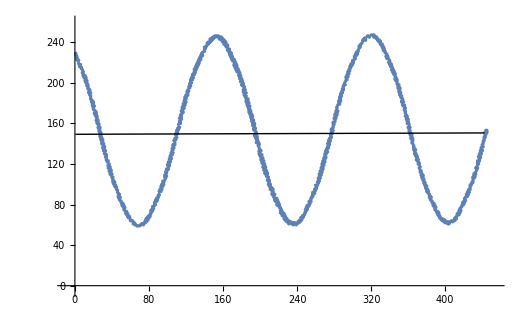

Plot::pllim: Range specification {x-1,0} is not of the form {x, xmin, xmax}.